## Ideal cylindrical hydro

```mathematica
hbarc=.19733;

(* Initial conditions *)
tau0Global=.4;

T0Global=.6/hbarc;
sigmaGlobal=2.;

LogT0[r_]:=Log[T0Global]-r^2/sigmaGlobal^2;
(*LogT0[r_]:=Log[Exp[-r^2/5^2](1+1000Exp[-r^2/3^2])]*)

(* Equation of state *)
cs2Global=1/3.;

(* Numerical solution *)
(* u^r(tau,r) = r H(tau,r) *)
sols=With[{cs2=cs2Global,T0=T0Global,tau0=tau0Global,sigma=sigmaGlobal},NDSolve[{Sqrt[1+r^2 H[tau,r]^2]D[LogT[tau,r],tau]+r H[tau,r]D[LogT[tau,r],r]==-cs2 (Sqrt[1+r^2 H[tau,r]^2]/tau+D[Sqrt[1+r^2 H[tau,r]^2],tau]+2 H[tau,r]+r D[H[tau,r],r]),Sqrt[1+r^2 H[tau,r]^2]r D[H[tau,r],tau]+r H[tau,r]D[r H[tau,r],r]==-D[LogT[tau,r],r]+r H[tau,r] cs2 (Sqrt[1+r^2 H[tau,r]^2]/tau+D[Sqrt[1+r^2 H[tau,r]^2],tau]+2 H[tau,r]+r D[H[tau,r],r]),LogT[tau0,r]==LogT0[r],H[tau0,r]==0},{LogT,H},{tau,tau0,50.},{r,0.00001,20},AccuracyGoal->5,PrecisionGoal->Infinity(*,InterpolationOrder->6*)]]
logTres=LogT/.sols[[1]];
Hres=H/.sols[[1]];
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable r. Artificial boundary effects may be present in the solution.

{{LogT→InterpolatingFunction[…],H→InterpolatingFunction[…]}}

## Temperature profile

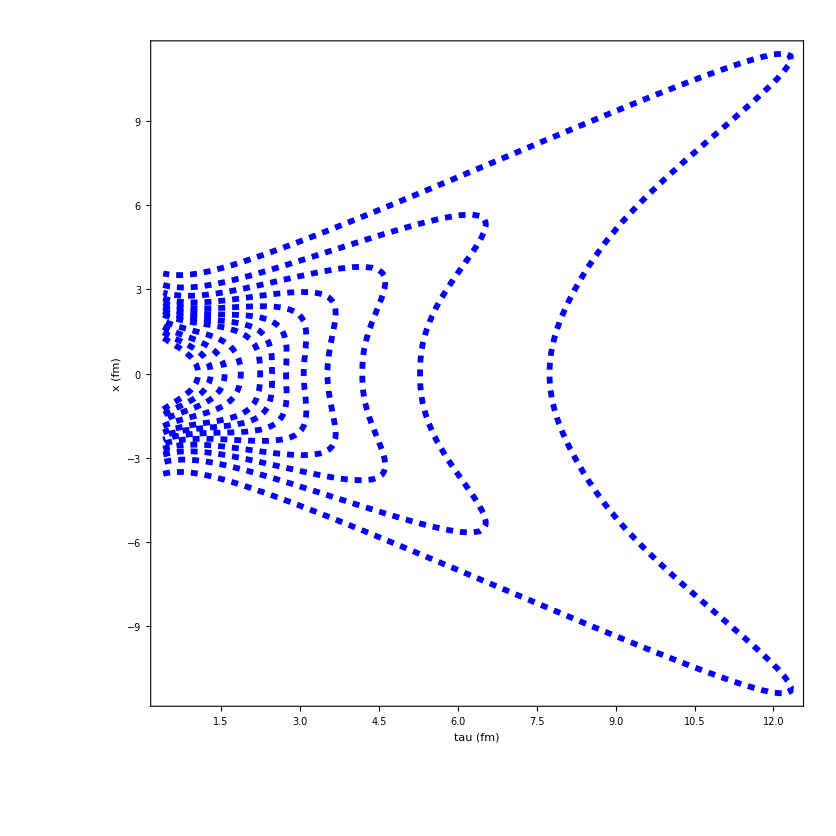

```mathematica
With[{tau0=tau0Global,taumax=40},
Show[
contourList={.025,.05,.075,.1,.125,.15,.175,.2,.25,.3,.35,.4};
(*ListContourPlot[Map[{#[[1]],Sqrt[#[[2]]^2+ysel^2],#[[3]]}&,Select[musicRaw,#[[3]]==ysel&][[;;,{1,2,4}]]],PlotRange->All,ContourShading->None,ContourStyle->{Directive[Red,Thickness[.01]]},Contours->contourList],*)
ContourPlot[Exp[logTres[tau,Abs[x]]]hbarc,{tau,tau0,taumax},{x,-15,15},PlotRange->All,ContourShading->None,ContourStyle->{{Blue,Thickness[.005],Dashed}},Contours->contourList,PlotPoints->100]
,PlotRange->All,FrameLabel->{"tau (fm)","x (fm)"}
]
]
```